```mathematica
cwdPath=NotebookDirectory[];
outPath=cwdPath<>"out/";
outPath="/home/michal/Documents/inz/results_sig-10_4C/resultset/";

s4K=4*1024;
s512K=512*1024;
s1M=2*s512K;
s4M=4*s1M;
s16M=16*s1M;
s32M=32*s1M;
s64M=64*s1M;
s128M=128*s1M;

gNodes={1,2,3,4,5,6,7,8,9,10};
gSizes={s4K,s512K,s1M,s4M,s16M,s32M,s64M};
gThred={1,2,3,4,5,6,7,8};
gActon={"create","read","update"};

MeanVal[iter_,data_]:={Mean[data],MeanDeviation[data]}/10^6/iter//N;
ParsePhase1[readListResult_]:={#1,#2,MeanVal[#3,#4]}&@@@readListResult;
ParsePhase2[threadsNum_,readListResult_]:=Prepend[#,threadsNum]&/@ParsePhase1[readListResult];
ParsePhase3[action_]:=ParsePhase2[#,ReadList[outPath<>action<>"-"<>ToString[#]<>"n.log"]]&/@gNodes//Flatten[#,1]&;
(*Result:{{nodes,size,threads,{mean,stddev}},...}*)

RawDataCreate=ParsePhase3["create"];
RawDataRead=ParsePhase3["read"];
RawDataUpdate=ParsePhase3["update"];

GetData[collection_,node_,size_,thrd_]:=Cases[collection,{node,size,thrd,_}][[1]][[4]];
GetCreate[node_,size_,thrd_]:=GetData[RawDataCreate,node,size,thrd];
GetRead[node_,size_,thrd_]:=GetData[RawDataRead,node,size,thrd];
GetUpdate[node_,size_,thrd_]:=GetData[RawDataUpdate,node,size,thrd];

GetSeriesInNodes[collection_,nodes_,size_,thrd_]:={#,GetData[collection,#,size,thrd][[1]]}&/@nodes;
GetSeriesInSizes[collection_,node_,sizes_,thrd_]:={#,GetData[collection,node,#,thrd][[1]]}&/@sizes;
GetSeriesInThrds[collection_,node_,size_,thrds_]:={#,GetData[collection,node,size,#][[1]]}&/@thrds;

GetCreateSeriesInNodes[n_,s_,t_]:=GetSeriesInNodes[RawDataCreate,n,s,t];
GetCreateSeriesInSizes[n_,s_,t_]:=GetSeriesInSizes[RawDataCreate,n,s,t];
GetCreateSeriesInThrds[n_,s_,t_]:=GetSeriesInThrds[RawDataCreate,n,s,t];

GetReadSeriesInNodes[n_,s_,t_]:=GetSeriesInNodes[RawDataRead,n,s,t];
GetReadSeriesInSizes[n_,s_,t_]:=GetSeriesInSizes[RawDataRead,n,s,t];
GetReadSeriesInThrds[n_,s_,t_]:=GetSeriesInThrds[RawDataRead,n,s,t];

GetUpdateSeriesInNodes[n_,s_,t_]:=GetSeriesInNodes[RawDataUpdate,n,s,t];
GetUpdateSeriesInSizes[n_,s_,t_]:=GetSeriesInSizes[RawDataUpdate,n,s,t];
GetUpdateSeriesInThrds[n_,s_,t_]:=GetSeriesInThrds[RawDataUpdate,n,s,t];
```

```mathematica
PrettyPlot[series_,plotLabel_,legendLabel_,axesLabel_]:=ListLinePlot[
#2&@@@series,
(*PlotTheme->"Scientific",*)
PlotLabel->plotLabel,
Filling->Axis,
AxesOrigin->{0,0},
PlotMarkers->{Automatic,10},
Frame->True,
FrameLabel->axesLabel,
LabelStyle->{FontColor->Black,FontSize->15},
GridLines->Automatic,
GridLinesStyle->Directive[LightGray,Dashed],
AspectRatio->1/GoldenRatio,
InterpolationOrder->None,
PlotLegends->Placed[
LineLegend[
{#1&@@@series},
LegendLabel-> legendLabel
],{0.75,0.75}]
];
```

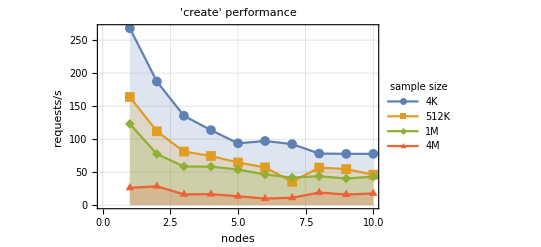
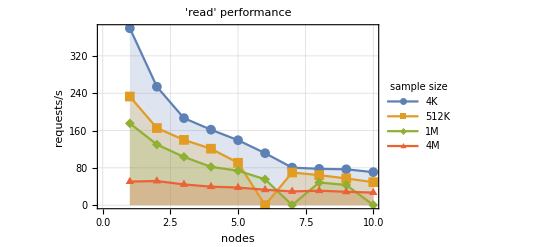
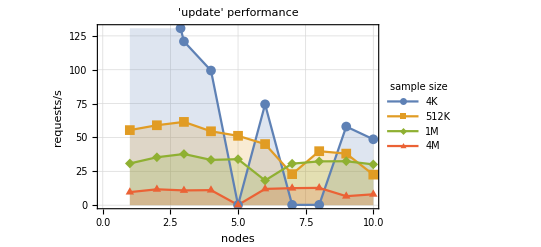

```mathematica
PrettyPlot[
{
{"4K",{#1,1/#2}&@@@GetSeriesInNodes[#1, gNodes,s4K,gThred[[4]]]},
{"512K",{#1,1/#2}&@@@GetSeriesInNodes[#1,gNodes,s512K,gThred[[4]]]},
{"1M",{#1,1/#2}&@@@GetSeriesInNodes[#1,gNodes,s1M,gThred[[4]]]},
{"4M",{#1,1/#2}&@@@GetSeriesInNodes[#1,gNodes,s4M,gThred[[4]]]}
},
#2,
"sample size",
{"nodes","requests/s"}
]&@@@{
{RawDataCreate,"'create' performance"},
{RawDataRead,"'read' performance"},
{RawDataUpdate,"'update' performance"}
}
```

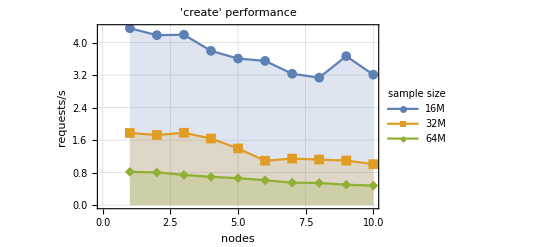
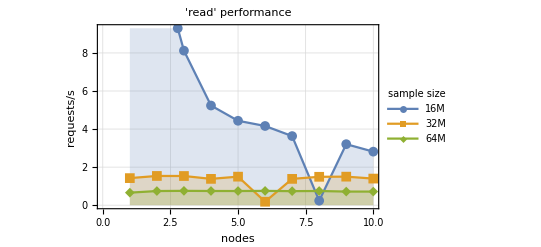
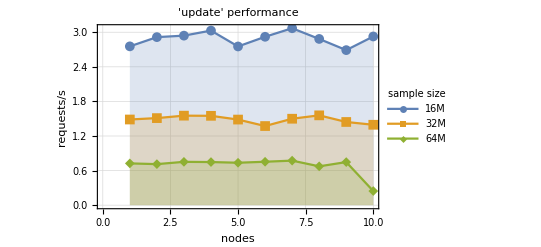

```mathematica
PrettyPlot[
{
(*{"4M",{#1,1/#2}&@@@GetSeriesInNodes[#1, gNodes,s4M,gThred[[4]]]},*)
{"16M",{#1,1/#2}&@@@GetSeriesInNodes[#1,gNodes,s16M,gThred[[4]]]},
{"32M",{#1,1/#2}&@@@GetSeriesInNodes[#1,gNodes,s32M,gThred[[4]]]},
{"64M",{#1,1/#2}&@@@GetSeriesInNodes[#1,gNodes,s64M,gThred[[4]]]}
},
#2,
"sample size",
{"nodes","requests/s"}
]&@@@{
{RawDataCreate,"'create' performance"},
{RawDataRead,"'read' performance"},
{RawDataUpdate,"'update' performance"}
}
```

```mathematica
PrettyPlot[
{
{"4K",{#1,1/#2}&@@@GetSeriesInNodes[#1, 4,gNodes,gThred[[1]]]},
{"512K",{#1,1/#2}&@@@GetSeriesInNodes[#1,gNodes,s4M,gThred[[2]]]},
{"1M",{#1,1/#2}&@@@GetSeriesInNodes[#1,gNodes,s4M,gThred[[3]]]},
{"4M",{#1,1/#2}&@@@GetSeriesInNodes[#1,gNodes,s4M,gThred[[4]]]}
},
#2,
"sample size",
{"nodes","requests/s"}
]&@@@{
{RawDataCreate,"'create' performance"},
{RawDataRead,"'read' performance"},
{RawDataUpdate,"'update' performance"}
}
```

ListLinePlot::lpn: {4., {{1., 59.395}, {2., 44.4327}, {3., 39.4351}, {4., 36.0808}, {5., 31.0619}, {6., 24.2425}, {7., 21.6793}, {8., 29.5162}, {9., 29.2604}, {10., 29.3457}}, {{1., 19.3585}, {2., 31.7314}, « 7 », {10., 23.4409}}, {{1., 26.2362}, {2., 28.6111}, {3., 16.3812}, {4., 16.6905}, {5., 13.5269}, {6., 9.99425}, {7., 11.1866}, {8., 19.1484}, {9., 16.0644}, {10., 17.7481}}} is not a list of numbers or pairs of numbers.

General::stop: Further output of ListLinePlot :: lpn will be suppressed during this calculation.

{ListLinePlot[{4,{{1,59.395},{2,44.4327},{3,39.4351},{4,36.0808},{5,31.0619},{6,24.2425},{7,21.6793},{8,29.5162},{9,29.2604},{10,29.3457}},{{1,19.3585},{2,31.7314},{3,15.9369},{4,23.3583},{5,17.9008},{6,17.5146},{7,17.4901},{8,25.6411},{9,23.0076},{10,23.4409}},{{1,26.2362},{2,28.6111},{3,16.3812},{4,16.6905},{5,13.5269},{6,9.99425},{7,11.1866},{8,19.1484},{9,16.0644},{10,17.7481}}},PlotLabel→'create' performance,Filling→Axis,AxesOrigin→{0,0},PlotMarkers→{Automatic,10},Frame→True,FrameLabel→{nodes,requests/s},LabelStyle→{FontColor→-Graphics-,FontSize→15},GridLines→Automatic,GridLinesStyle→Directive[-Graphics-,Dashing[{Small,Small}]],AspectRatio→1/GoldenRatio,InterpolationOrder→None,PlotLegends→Placed[LineLegend[{{4K,512K,1M,4M}},LegendLabel→sample size],{0.75,0.75}]],ListLinePlot[{4,{{1,78.7245},{2,76.2079},{3,66.8545},{4,65.6085},{5,60.4165},{6,58.7247},{7,53.652},{8,47.5981},{9,0.265723},{10,46.1554}},{{1,60.0205},{2,65.3892},{3,54.3485},{4,44.3714},{5,47.6306},{6,44.2024},{7,40.0477},{8,38.672},{9,32.639},{10,0.284471}},{{1,50.5456},{2,51.7769},{3,44.441},{4,39.6877},{5,37.7536},{6,33.0593},{7,29.3954},{8,31.0837},{9,28.6234},{10,27.0001}}},PlotLabel→'read' performance,Filling→Axis,AxesOrigin→{0,0},PlotMarkers→{Automatic,10},Frame→True,FrameLabel→{nodes,requests/s},LabelStyle→{FontColor→-Graphics-,FontSize→15},GridLines→Automatic,GridLinesStyle→Directive[-Graphics-,Dashing[{Small,Small}]],AspectRatio→1/GoldenRatio,InterpolationOrder→None,PlotLegends→Placed[LineLegend[{{4K,512K,1M,4M}},LegendLabel→sample size],{0.75,0.75}]],ListLinePlot[{4,{{1,23.0798},{2,21.8678},{3,14.9482},{4,21.388},{5,22.0632},{6,21.4634},{7,0.220939},{8,19.8809},{9,21.3926},{10,21.2905}},{{1,12.0237},{2,16.0664},{3,15.5228},{4,16.4823},{5,16.4885},{6,12.9119},{7,14.2581},{8,11.5844},{9,13.3064},{10,0.279139}},{{1,9.64002},{2,11.7167},{3,10.9044},{4,11.1071},{5,0.165818},{6,12.0076},{7,12.5636},{8,12.7866},{9,6.63133},{10,8.04107}}},PlotLabel→'update' performance,Filling→Axis,AxesOrigin→{0,0},PlotMarkers→{Automatic,10},Frame→True,FrameLabel→{nodes,requests/s},LabelStyle→{FontColor→-Graphics-,FontSize→15},GridLines→Automatic,GridLinesStyle→Directive[-Graphics-,Dashing[{Small,Small}]],AspectRatio→1/GoldenRatio,InterpolationOrder→None,PlotLegends→Placed[LineLegend[{{4K,512K,1M,4M}},LegendLabel→sample size],{0.75,0.75}]]}